```mathematica
Clear["Global`*"]
```

```mathematica
(*Hamiltonian using QuFoTr*)
HamiltonianJLP[ns_,phiMax_, omega_]:=Module[
{deltaPhi,beta,phi,phi2,kmax,deltaK,betak,k,F,Pik2,Piphi2,H},

(*each of the phi and pi matricies (position and momentum equivalents) and diagonal in their own space,we apply the QuFoTr to the matricies to move back and forth*)

deltaPhi=2 phiMax/(ns-1);
beta=Range[0,ns-1];
phi=-phiMax+beta deltaPhi;
phi2=DiagonalMatrix[phi^2];(*diagonal phi squared matrix in the field space*)

kmax=Pi/deltaPhi;
deltaK=2 Pi/(deltaPhi ns);
betak=Range[0,ns-1];
k=-kmax+betak deltaK;

F=Exp[-I Outer[Times,k,phi]]/Sqrt[ns]; (*creates a unitary Fourier matrix that transforms between the field basis and the momentum basis F phi->K*)

Pik2=DiagonalMatrix[k^2];(*diagonal pi squared matrix in momentum space*)

Piphi2=ConjugateTranspose[F].Pik2.F;(*pi squared matrix in field space*)

H=0.5 (omega^2 phi2+Piphi2);(*Hamiltonian*)
(*might end up being slightly none hermitian because computers so:*)
H=0.5 (H+ConjugateTranspose[H]);

{H,phi}
];

(*Precision Function*)

FindPrecision[method_,ns_,phiMax_, omega_]:=Module[
{H,ordereig,eiglow,eigexact,relerror},(*choose Hamiltonian type based on method*)

{H,_}=Which[method=="FD",HamiltonianFD[ns,phiMax],method == "JLP", HamiltonianJLP[ns,phiMax, omega], method == "FDcorrected", HamiltonianFDCorrected[ns, phiMax], True, Return[$Failed, Module]];
ordereig=Sort[Re[Eigenvalues[H]]];
eiglow=ordereig[[1;;Min[5,Length[ordereig]]]];(*gets five lowest eigenvalues of hamiltonian like in savage*)
eigexact=omega(Range[0,4]+0.5);(*gets exact HO energies*)
relerror=Abs[(eiglow-eigexact)/eigexact]*100;
relerror];

(*Automated results get*)

ComputeResults[method_,nqList_,phiMaxValues_,omega_]:=Module[
{results=Association[],ns},
Do[ns=2^nq;
results[nq]=Table[{phiMax,FindPrecision[method,ns,phiMax,omega]},{phiMax,phiMaxValues}];,
{nq,nqList}];(*loops over each nq in nqlist based on the chosen method*)
results];

(*Plotting Functions*)

PlotResults[results_,title_String:"Relative Errors for First Energy Level (JLP Hamiltonian)"]:=Module[
{plotGroups,colorList,allCurves,legendLabels,plt},

plotGroups=Table[Table[Table[(*still dont really get why I had to do table 3 times*)
{results[nq][[i,1]],results[nq][[i,2,j]]},{i,Length[results[nq]]}],{j,5}],
{nq,nqList} ];(*loops over each nq in the nq list for each of the errors in each energy level*)

colorList={Blue,Red,Green};(*colours*)

allCurves= Flatten[Table[Table[Style[Table[(*know why I need flatten and style but why I need three table things is beyond me*)
{results[nqList[[m]]][[i,1]],results[nqList[[m]]][[i,2,j]]},{i,Length[results[nqList[[m]]]]}],colorList[[m]],Thick],{j,1}],(*j loops over the nq indicies (energy levels)*){m,Length[nqList]}],1 (*again iteration stuff*)];

legendLabels=Table["nQ = "<>ToString[nqList[[m]]],{m,Length[nqList]}];(*makes the legend labels*)

plt=ListLogPlot[allCurves,(*plots as log log graph and which data to plot*)
Joined->True,(*should the data be connected with lines*)
Frame->True,(*Full Frame instead of standard axis*)
FrameLabel->{"ϕmax","relative error (%)"},(*axis labels*)
PlotLegends->Placed[LineLegend[colorList,legendLabels,LegendMarkerSize->30],Below],(*adds legend with labels and size and colour*)
GridLines->Automatic,(*Background gridlines*)
PlotLabel->Style[title,16],(*title*)
ImageSize->Large,PlotRange->All];(*makes sure all of the data is included*)

plt];


optimalPhiMax[nphi_,omega_:1] := (1/Sqrt[omega]) Sqrt[(Pi/2)*((nphi-1)^2/nphi)];
```

1

{(7 √π)/4,(15 √(π/2))/4,(31 √π)/8}

Set::nosym: _ does not contain a symbol to attach a rule to.

General::stop: Further output of Set::nosym will be suppressed during this calculation.

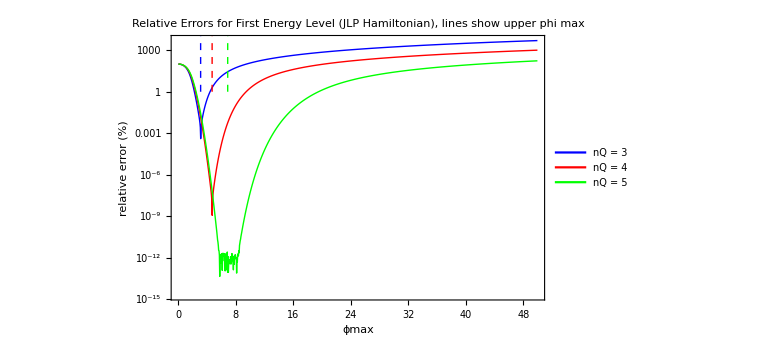

```mathematica
nqList={3,4,5};
phiMaxValues=Range[0.01,50,0.05];
w=1
optimalPhiMaxList = {};
For[i=1, i<=Length[nqList], i++, AppendTo[optimalPhiMaxList, optimalPhiMax[2^nqList[[i]],w]]]
optimalPhiMaxList

resultsJLP=ComputeResults["JLP",nqList,phiMaxValues,w];
plotJLP=PlotResults[resultsJLP,"Relative Errors for First Energy Level (JLP Hamiltonian), lines show upper phi max"];


colors={Blue,Red,Green};

Show[plotJLP,Epilog->Flatten[Table[{colors[[i]],Dashed,Thick,Line[{{optimalPhiMaxList[[i]],10^-12},{optimalPhiMaxList[[i]],100}}]},{i,Length[optimalPhiMaxList]}]]]
```